# Краен изпит на Светослав Добромиров Славов, Фак. №2001261051

## Задача 4.

```mathematica
DSolve[{y'[x]==y[x]-(5+1)Cos[x], y[3]==1}, y[x],x]
```

{{y[x]→(ⅇ^x-3 ⅇ^x Cos[3]+3 ⅇ^3 Cos[x]+3 ⅇ^x Sin[3]-3 ⅇ^3 Sin[x])/ⅇ^3}}

Мрежата е с n = 4 и стъпка h = 0.025

Теоретичната локална грешка  е 0.000015625

Теоретичната глобална грешка е 0.000625

i = 0, x_i = 3., y_i = 1., f_i = 6.93995, x_(i + 1/2) = 3.0125, y_(i + 1/2) = 1.08675, f_(i + 1/2) = 7.03682 , y_точно = 1., истинска грешка = 4.44089×10^-16

i = 1, x_i = 3.025, y_i = 1.17592, f_i = 7.13519, x_(i + 1/2) = 3.0375, y_(i + 1/2) = 1.26511, f_(i + 1/2) = 7.23263 , y_точно = 1.17594, истинска грешка = 0.0000164342

i = 2, x_i = 3.05, y_i = 1.35674, f_i = 7.33159, x_(i + 1/2) = 3.0625, y_(i + 1/2) = 1.44838, f_(i + 1/2) = 7.42962 , y_точно = 1.35677, истинска грешка = 0.0000333946

i = 3, x_i = 3.075, y_i = 1.54248, f_i = 7.52918, x_(i + 1/2) = 3.0875, y_(i + 1/2) = 1.63659, f_(i + 1/2) = 7.62782 , y_точно = 1.54253, истинска грешка = 0.0000508989

i = 4, x_i = 3.1, y_i = 1.73317, f_i = 7.72798, x_(i + 1/2) = 3.1125, y_(i + 1/2) = 1.82977, f_(i + 1/2) = 7.82723 , y_точно = 1.73324, истинска грешка = 0.0000689657

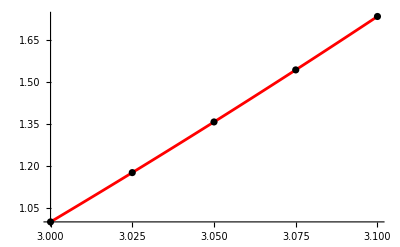

```mathematica
(*Въвеждаме условието на задачата*)
a = 3.;b=3.1;
x = a;
y = 1.;
points = {{x,y}};
f[x_,y_] :=y-(5+1)Cos[x]

(*Точно решение*)
yt[x_] := (ⅇ^x-3 ⅇ^x Cos[3]+3 ⅇ^3 Cos[x]+3 ⅇ^x Sin[3]-3 ⅇ^3 Sin[x])/ⅇ^3

(*Съставяме мрежата*)
n = 4; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]

(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, ", x_i = ", x, ", y_i = ", y, ", f_i = ", f[x,y]  , ", x_(i + 1/2) = ", x12, ", y_(i + 1/2) = ", y12, ", f_(i + 1/2) = ", f[x12,y12]  ", y_(:0442:043e:0447:043d:043e) = ", yt[x], ", истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]

(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

г) точно решение

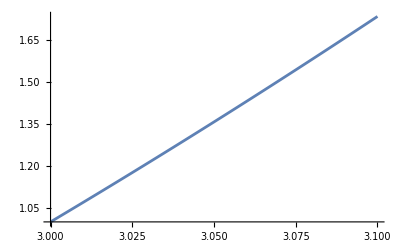

```mathematica
yt[x_]:= (ⅇ^x-3 ⅇ^x Cos[3]+3 ⅇ^3 Cos[x]+3 ⅇ^x Sin[3]-3 ⅇ^3 Sin[x])/ⅇ^3
Plot[yt[x], {x, a,b}]
```

### д) По метод на Рунге-Кута с четири междинни точки да се реши приближено задачата със същата стъпка. Запишете резултатите в таблица. Сравнете с точното решение.

Мрежата е с n = 4 и стъпка h = 0.025

Теоретичната локална  грешка е 9.76563×10^-9

Теоретичната глобална грешка е 3.90625×10^-7

i = 0, x_i = 3., y_i = 1., k1 = 0.173499, k2 = 0.175921, k3 = 0.175951, k4 = 0.17838, y_точно = 1., истинска грешка = 4.44089×10^-16

i = 1, x_i = 3.025, y_i = 1.17594, k1 = 0.17838, k2 = 0.180816, k3 = 0.180847, k4 = 0.183291, y_точно = 1.17594, истинска грешка = 7.24323×10^-10

i = 2, x_i = 3.05, y_i = 1.35677, k1 = 0.18329, k2 = 0.185741, k3 = 0.185772, k4 = 0.188231, y_точно = 1.35677, истинска грешка = 1.47312×10^-9

i = 3, x_i = 3.075, y_i = 1.54253, k1 = 0.188231, k2 = 0.190697, k3 = 0.190728, k4 = 0.193202, y_точно = 1.54253, истинска грешка = 2.24701×10^-9

i = 4, x_i = 3.1, y_i = 1.73324, k1 = 0.193201, k2 = 0.195683, k3 = 0.195714, k4 = 0.198203, y_точно = 1.73324, истинска грешка = 3.04664×10^-9

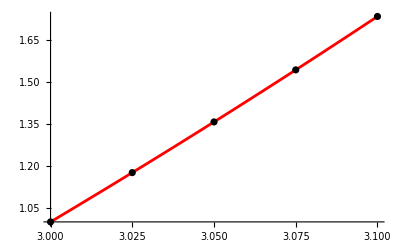

```mathematica
(*Въвеждаме условието на задачата*)
a = 3.;b=3.1;
x = a;
y = 1.;
points = {{x,y}};
f[x_,y_] :=y-(5+1)Cos[x]

(*Точно решение*)
yt[x_] := (ⅇ^x-3 ⅇ^x Cos[3]+3 ⅇ^3 Cos[x]+3 ⅇ^x Sin[3]-3 ⅇ^3 Sin[x])/ⅇ^3

(*Съставяме мрежата*)
n = 4; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]

(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1=h*f[x,y];
k2=h*f[x+1/2 h,y+1/2 k1];
k3=h*f[x+1/2 h,y+1/2 k2];
k4=h*f[x+h,y+k3];
Print["i = ", i, ", x_i = ",x, ", y_i = ",y, ", k1 = ",k1,", k2 = ",k2,", k3 = ",k3,", k4 = ",k4,", y_(:0442:043e:0447:043d:043e) = ", yt[x], ", истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2k2+2k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]

(*Визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```